/Users/steven/Nextcloud/NetDisk/Works/24.08.19 NonBoltz/Code/scale

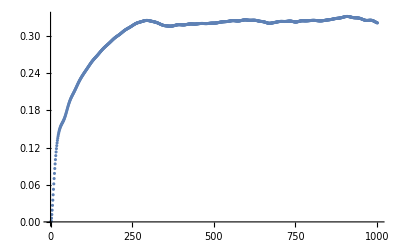

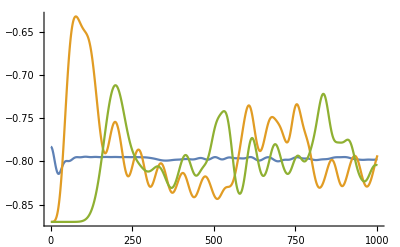

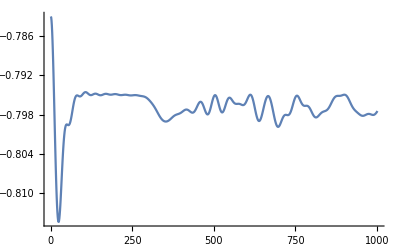

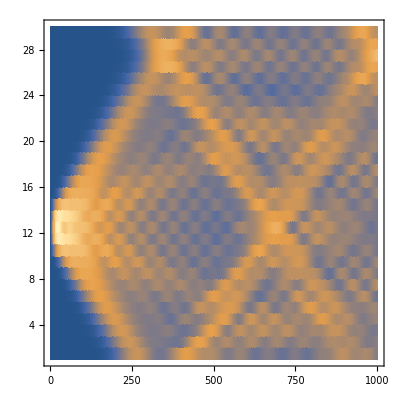

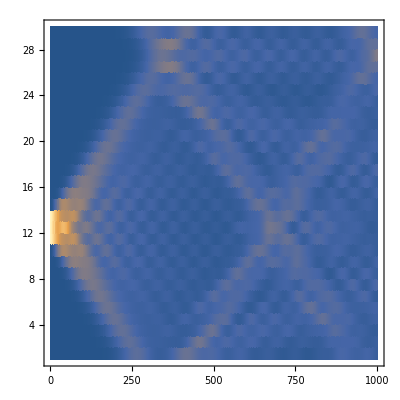

snt.csv

pnt.csv

Et.csv

```mathematica
SetDirectory[NotebookDirectory[]]
(*Tmax=0.3/J*20;*)
Tnum=1000;
(*Tmax=.8Tmax;*)

Pnat=Import["N30.wdx"];
a=2;NN=30;
Tnum=Length[Pnat⟦1,1,;;⟧];
EntroS[P_]:=Sum[
If[0<P⟦n⟧<1,-P⟦n⟧Log[P⟦n⟧],0],{n,1,Length[P]}];
Snt=ParallelTable[EntroS[Pnat⟦n,;;,t⟧],
{n,1,NN},{t,1,Tnum}]; (* Entropy Subscript[S, n](t) *)
St=1/NN Table[Total[Snt⟦;;,t⟧],{t,1,Tnum}];
DDt=1/NN Table[Total[Pnat⟦;;,1,t⟧+Pnat⟦;;,3,t⟧],{t,1,Tnum}];
Pat=1./NN Table[Total[Pnat⟦;;,a,t⟧],{a,1,3},{t,1,Tnum}];
J=0.3;Ω=-1;ω=-0.13;
E0=0.; Ep1=Ω+ω; Em1=Ω-ω;
Et=Em1*Pat⟦1,;;⟧+E0*Pat⟦2,;;⟧+Ep1*Pat⟦3,;;⟧;
Et1=Em1*Pnat⟦5,1,;;⟧+E0*Pnat⟦5,2,;;⟧+Ep1*Pnat⟦5,3,;;⟧;
Et2=Em1*Pnat⟦10,1,;;⟧+E0*Pnat⟦10,2,;;⟧+Ep1*Pnat⟦10,3,;;⟧;

Dt1=Pnat⟦5,1,;;⟧+Pnat⟦5,3,;;⟧;
Dt2=Pnat⟦10,1,;;⟧+Pnat⟦10,3,;;⟧;
Snt=RotateLeft[Snt,20];
pt=RotateLeft[Pnat⟦;;,2,;;⟧,20];
ListPlot[St,PlotRange->All]
(*ListPlot[{DDt,Dt1,Dt2},PlotRange->All,Joined->True]*)
ListPlot[{Et,Et1,Et2},PlotRange->All,Joined->True]
ListPlot[Et,PlotRange->All,Joined->True]
ListDensityPlot[Snt,PlotRange->All,InterpolationOrder->0]
ListDensityPlot[pt,PlotRange->All,InterpolationOrder->0]

Export["snt.csv",Snt,"CSV"]
Export["pnt.csv",pt,"CSV"]
Export["Et.csv",{Et,Et1,Et2},"CSV"]
```

```mathematica
Dimensions[Pat]
```

{3,1001}

```mathematica
ftSnt=Fourier[Snt];
ftSnt=RotateRight[ftSnt,{15,Floor[Tnum/2]}];
```

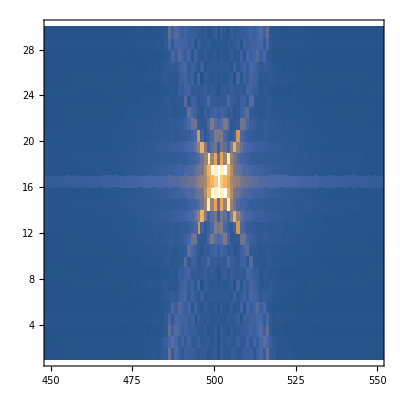

```mathematica
ListDensityPlot[Abs[ftSnt],InterpolationOrder->0,PlotRange->{{450,550},All,{0,5}}]
```